

```mathematica
Plot[x,{x,-2,2}]
```

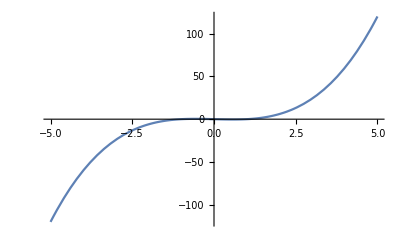

```mathematica
Plot[x^3-x,{x,-5,5}]
```

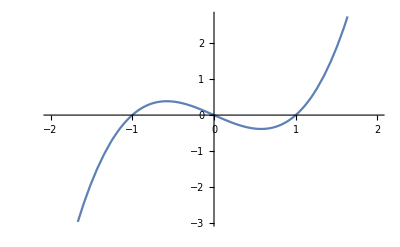

```mathematica
Plot[x^3-x,{x,-2,2}]
```

```mathematica
Manipulate[
Plot[x^3+a x,{x,-2,2}],{a,-1,1}]
```

```mathematica
Manipulate[Plot[(1-a)x+a x^2,{x,-2,2}],{a,0,1}]
```

```mathematica
Manipulate[Plot[x^(1-a)+ (x^2)^a,{x,-2,2}],{a,0,1}]
```

```mathematica
Manipulate[Plot[x^(1-a) (x^2)^a,{x,-2,2}],{a,0,1}]
```

```mathematica
Manipulate[Plot[x x^a,{x,-2,2}],{a,0,1}]
```

```mathematica
Manipulate[Plot[{Abs[x],x x^a},{x,-2,2}],{a,0,1}]
```

```mathematica
x^3-x==0
```

-x+x^3==0

```mathematica
FindInstance[-x+x^3==0,{x}]
```

{{x→0}}

```mathematica
Reduce[-x+x^3==0]
```

x==-1||x==0||x==1

```mathematica
x^4-x^2
```

-x^2+x^4

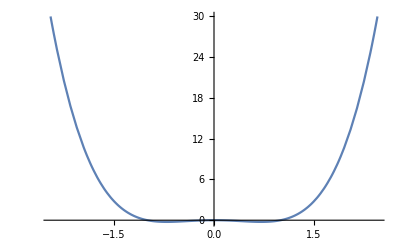

```mathematica
Plot[-x^2+x^4,{x,-2.449489742783178,2.449489742783178}]
```

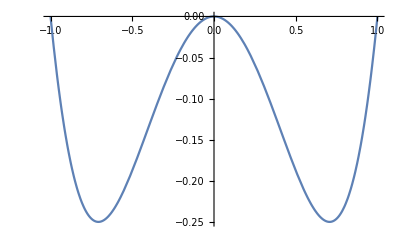

```mathematica
Plot[-x^2+x^4,{x,-1,1}]
```

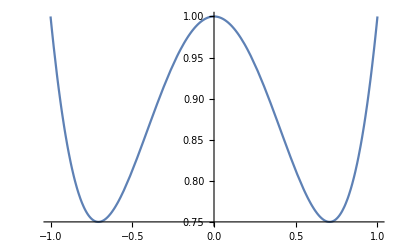

```mathematica
Plot[-x^2+x^4+1,{x,-1,1}]
```

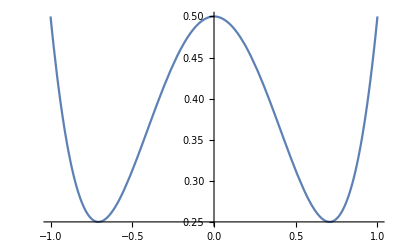

```mathematica
Plot[-x^2+x^4+1/2,{x,-1,1}]
```

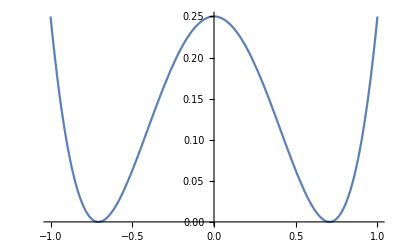

```mathematica
Plot[-x^2+x^4+1/4,{x,-1,1}]
```

```mathematica
Plot[-x^2+x^4,{x,-1,1}]
```

-Graphics-

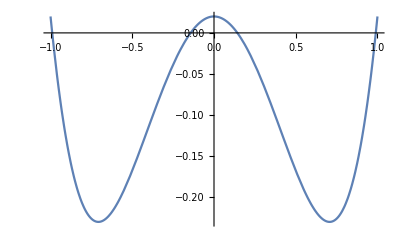

```mathematica
Plot[-x^2+x^4+1/50,{x,-1,1}]
```

```mathematica
Normalize@{x,x^3-x}.(Normalize@{x,x} RotationMatrix[θ])
```

{(x^2 Cos[θ])/(√2 Abs[x] √(Abs[x]^2+Abs[-x+x^3]^2))+(x (-x+x^3) Sin[θ])/(√2 Abs[x] √(Abs[x]^2+Abs[-x+x^3]^2)),(x (-x+x^3) Cos[θ])/(√2 Abs[x] √(Abs[x]^2+Abs[-x+x^3]^2))-(x^2 Sin[θ])/(√2 Abs[x] √(Abs[x]^2+Abs[-x+x^3]^2))}

```mathematica
FullSimplify[Normalize@{x,x^3-x}.(Normalize@{x,x} RotationMatrix[θ]),{x,θ}∈Reals]
```

{(Cos[θ]+(-1+x^2) Sin[θ])/(√2 √(2-2 x^2+x^4)),((-1+x^2) Cos[θ]-Sin[θ])/(√2 √(2-2 x^2+x^4))}

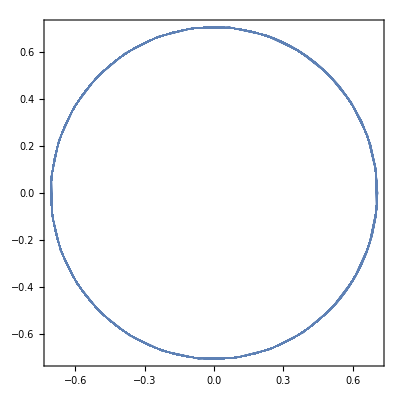

```mathematica
ParametricPlot[
{(Cos[θ]+(-1+x^2) Sin[θ])/(√2 √(2-2 x^2+x^4)),((-1+x^2) Cos[θ]-Sin[θ])/(√2 √(2-2 x^2+x^4))}
,{x,-2,2},{θ,-2π,2π}]
```

```mathematica
Manipulate[
ParametricPlot[
{(Cos[θ]+(-1+x^2) Sin[θ])/(√2 √(2-2 x^2+x^4)),((-1+x^2) Cos[θ]-Sin[θ])/(√2 √(2-2 x^2+x^4))}
,{x,-2,2}],{θ,-2π,2π}]
```

```mathematica
(Normalize@{x,x} RotationMatrix[θ])
```

{{(x Cos[θ])/(√2 Abs[x]),-(x Sin[θ])/(√2 Abs[x])},{(x Sin[θ])/(√2 Abs[x]),(x Cos[θ])/(√2 Abs[x])}}

```mathematica
Normalize@{x,x} .RotationMatrix[θ]
```

{(x Cos[θ])/(√2 Abs[x])+(x Sin[θ])/(√2 Abs[x]),(x Cos[θ])/(√2 Abs[x])-(x Sin[θ])/(√2 Abs[x])}

```mathematica
FullSimplify[Normalize@{x,x^3-x}.(Normalize@{x,x} .RotationMatrix[θ]),{x,θ}∈Reals]
```

(x^2 (Cos[θ]-Sin[θ])+2 Sin[θ])/(√2 √(2-2 x^2+x^4))

```mathematica
Manipulate[Plot[(x^2 (Cos[θ]-Sin[θ])+2 Sin[θ])/(√2 √(2-2 x^2+x^4)),{x,-0.6893412099579035,3.119105350530072}],{θ,-2.637314895538441,0.7759837560707786}]
```

```mathematica
Plot3D[
(x^2 (Cos[θ]-Sin[θ])+2 Sin[θ])/(√2 √(2-2 x^2+x^4)),{x,-2,2},{θ,-2π,2π}]
```

-Graphics3D-

```mathematica
Grad[(x^2 (Cos[θ]-Sin[θ])+2 Sin[θ])/(√2 √(2-2 x^2+x^4)),{x,θ}]
```

{(√2 x (Cos[θ]-Sin[θ]))/(√(2-2 x^2+x^4))-((-4 x+4 x^3) (x^2 (Cos[θ]-Sin[θ])+2 Sin[θ]))/(2 √2 (2-2 x^2+x^4)^(3/2)),(2 Cos[θ]+x^2 (-Cos[θ]-Sin[θ]))/(√2 √(2-2 x^2+x^4))}

```mathematica
Solve[{(√2 x (Cos[θ]-Sin[θ]))/(√(2-2 x^2+x^4))-((-4 x+4 x^3) (x^2 (Cos[θ]-Sin[θ])+2 Sin[θ]))/(2 √2 (2-2 x^2+x^4)^(3/2))==0,(2 Cos[θ]+x^2 (-Cos[θ]-Sin[θ]))/(√2 √(2-2 x^2+x^4))==0},{x,θ}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Solve::svars: Equations may not give solutions for all "solve" variables.

{{x→0,θ→-π/2},{x→0,θ→π/2}}

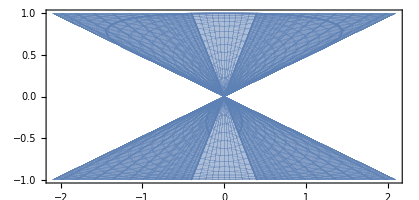

```mathematica
ParametricPlot[
{(√2 x (Cos[θ]-Sin[θ]))/(√(2-2 x^2+x^4))-((-4 x+4 x^3) (x^2 (Cos[θ]-Sin[θ])+2 Sin[θ]))/(2 √2 (2-2 x^2+x^4)^(3/2)),(2 Cos[θ]+x^2 (-Cos[θ]-Sin[θ]))/(√2 √(2-2 x^2+x^4))}
,{x,-2,2},{θ,0,2π}]
```

```mathematica
Plot3D[
{1,(x^2 (Cos[θ]-Sin[θ])+2 Sin[θ])/(√2 √(2-2 x^2+x^4))}
,{x,-2,2},{θ,-2π,2π}]
```

-Graphics3D-

```mathematica
Plot3D[
{.9,(x^2 (Cos[θ]-Sin[θ])+2 Sin[θ])/(√2 √(2-2 x^2+x^4))}
,{x,-2,2},{θ,-2π,2π}]
```

-Graphics3D-

```mathematica
VectorPlot3D[
{(√2 x (Cos[θ]-Sin[θ]))/(√(2-2 x^2+x^4))-((-4 x+4 x^3) (x^2 (Cos[θ]-Sin[θ])+2 Sin[θ]))/(2 √2 (2-2 x^2+x^4)^(3/2)),(2 Cos[θ]+x^2 (-Cos[θ]-Sin[θ]))/(√2 √(2-2 x^2+x^4))}
,{x,-2,2},{θ,-2π,2π}]
```

VectorPlot3D::argrx: VectorPlot3D called with 3 arguments; 4 arguments are expected.

VectorPlot3D[{(√2 x (Cos[θ]-Sin[θ]))/(√(2-2 x^2+x^4))-((-4 x+4 x^3) (x^2 (Cos[θ]-Sin[θ])+2 Sin[θ]))/(2 √2 (2-2 x^2+x^4)^(3/2)),(2 Cos[θ]+x^2 (-Cos[θ]-Sin[θ]))/(√2 √(2-2 x^2+x^4))},{x,-2,2},{θ,-2 π,2 π}]

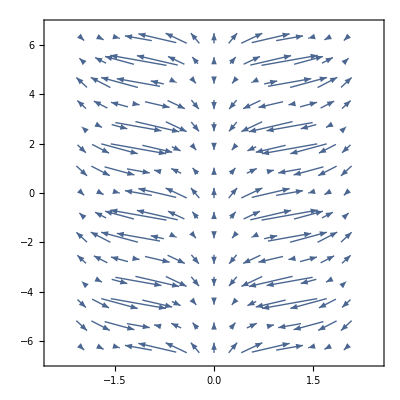

```mathematica
VectorPlot[
{(√2 x (Cos[θ]-Sin[θ]))/(√(2-2 x^2+x^4))-((-4 x+4 x^3) (x^2 (Cos[θ]-Sin[θ])+2 Sin[θ]))/(2 √2 (2-2 x^2+x^4)^(3/2)),(2 Cos[θ]+x^2 (-Cos[θ]-Sin[θ]))/(√2 √(2-2 x^2+x^4))}
,{x,-2,2},{θ,-2π,2π}]
```

```mathematica
Plot3D[
(x^2 (Cos[θ]-Sin[θ])+2 Sin[θ])/(√2 √(2-2 x^2+x^4)),{x,-2,2},{θ,-2π,2π}]
```

-Graphics3D-

```mathematica
GroebnerBasis[x^3-x,x]
```

{-x+x^3}

```mathematica
GroebnerBasis[x^3-x,{x}]
```

{-x+x^3}

```mathematica
FullSimplify[Normalize@{0,D[x^3-x,{x,2}]}.Normalize@{x,D[x^3-x,x]},x∈Reals]
```

(x (-1+3 x^2))/(√(x^2-5 x^4+9 x^6))

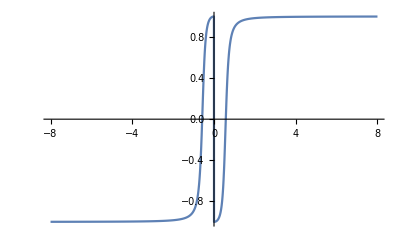

```mathematica
Plot[(x (-1+3 x^2))/(√(x^2-5 x^4+9 x^6)),{x,-8,8}]
```

```mathematica
Abs[(x (-1+3 x^2))/(√(x^2-5 x^4+9 x^6))]
```

Abs[(x (-1+3 x^2))/(√(x^2-5 x^4+9 x^6))]

```mathematica
FullSimplify[Abs[(x (-1+3 x^2))/(√(x^2-5 x^4+9 x^6))],x∈Reals]
```

Abs[1-3 x^2]/(√(1-5 x^2+9 x^4))

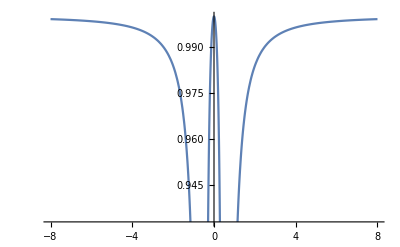

```mathematica
Plot[Abs[1-3 x^2]/(√(1-5 x^2+9 x^4)),{x,-8,8}]
```

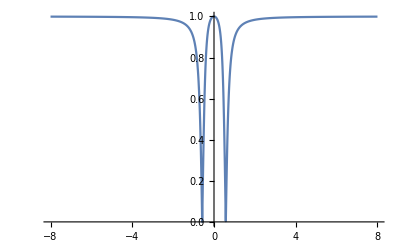

```mathematica
Plot[Abs[1-3 x^2]/(√(1-5 x^2+9 x^4)),{x,-8,8},PlotRange->Full]
```

```mathematica
FullSimplify[Normalize@{x,x^3-x},x∈Reals]
```

{x/(√(x^2+(x-x^3)^2)),(x (-1+x^2))/(√(x^2+(x-x^3)^2))}

```mathematica
Manipulate[
ParametricPlot[{
{x/(√(x^2+(x-x^3)^2)),(x (-1+x^2))/(√(x^2+(x-x^3)^2))},
{x,x^3-x}
},{x,-3+a,-2+a}]
,{a,0,6}]
```

```mathematica
Manipulate[
ParametricPlot[{
{x/(√(x^2+(x-x^3)^2)),(x (-1+x^2))/(√(x^2+(x-x^3)^2))},
{x,x^3-x}
},{x,-3+a,-2+a},PlotRange->{{-2,2},{-2,2}}]
,{a,0,6}]
```

```mathematica
Manipulate[
ParametricPlot[{
{x/(√(x^2+(x-x^3)^2)),(x (-1+x^2))/(√(x^2+(x-x^3)^2))},
{x,x^3-x}
},{x,-3,-3+a},PlotRange->{{-2,2},{-2,2}}]
,{a,0,6}]
```

ParametricPlot::plld: Endpoints for x in {x,-3,-3+FE`a$$291} must have distinct machine-precision numerical values.

General::stop: Further output of ParametricPlot::plld will be suppressed during this calculation.